```mathematica
f[x_]:=a Sin[b x]+c Cos[d x]+Cos[x]+4.5
a=1.4
b=3
c=1.2
d=4.5
N[Solve[f'[x+4.077]==0&&x>0&&x<5,x, Reals]]
x0=1.1
x1=2.031982161048468
x2=3.690200140461272
x3=0.8924904834689227
off=0.2
s=15
s1=15
Plot[f[x+4.077],{x,0,5}, Ticks->None, Epilog->{Point[{x0,f[x0+4.077]}],Text[Style["C",s],{x0,f[x0+4.077]+off},{0,-1}],Point[{x1,f[x1+4.077]}],Text[Style["C_1",s],{x1,f[x1+4.077]+off},{0,-1}],Point[{x2,f[x2+4.077]}],Text[Style["C_0",s],{x2,f[x2+4.077]+off},{0,-1}],Point[{x3,f[x3+4.077]}],Text[Style["C_2",s],{x3,f[x3+4.077]+off},{0,-1}]}, FrameLabel->{Style["Configuraciones",s1], Style["F",s1]}]
```

## Hexagonos

0.06

-Graphics-

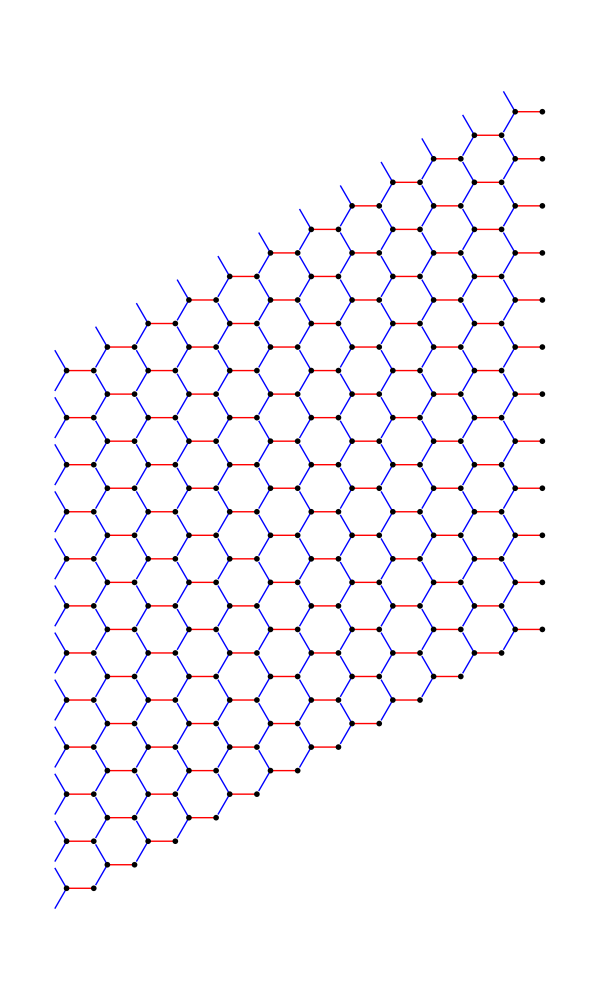

```mathematica
tam=0.06
unitCell[x_,y_]:={Red,Line[{{x,y},{x+2/3 Sin[120 Degree],y}}],Blue,Line[{{x,y},{x-Sin[30 Degree]/2,y+Cos[30 Degree]/2}}],Blue,Line[{{x,y},{x-Sin[30 Degree]/2,y-Cos[30 Degree]/2}}],Black,Disk[{x,y},tam],Black,Disk[{x+2/3 Sin[120 Degree],y},tam]}
Graphics[unitCell[0,0],ImageSize->100]
Graphics[Block[{unitVectA={Sin[60Degree],Cos[60Degree]},unitVectB={0,1}},Table[unitCell@@(unitVectA j+unitVectB k),{j,-12,-1},{k,1,12}]],ImageSize->600]
```

```mathematica
Ç
```

Cuadrados

0.06

-Graphics-

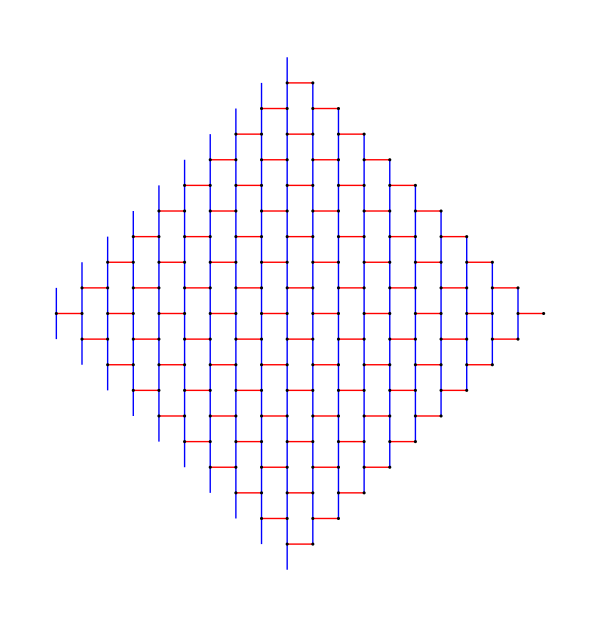

```mathematica
tam=0.06
unitCell2[x_,y_]:={Red,Line[{{x,y},{x+1,y}}],Blue,Line[{{x,y},{x,y+1}}],Blue,Line[{{x,y},{x,y-1}}],Black,Disk[{x,y},tam],Black,Disk[{x+1,y},tam]}
Graphics[unitCell2[0,0],ImageSize->100]
Graphics[Block[{unitVectA={-1,1},unitVectB={-1,-1}},Table[unitCell2@@(unitVectA j+unitVectB k),{j,-10,-1},{k,1,10}]],ImageSize->600]
```